```mathematica
Clear[Derivative]

DE=y'[t]-k*y[t]*(1- y[t]/K)==0
IC={y[0]==2}
Gensol = DSolve[{DE, IC}, y[t], t]
Parsol=DSolve[{DE,IC},y[t],t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}]
```

-k y[t] (1-y[t]/K)+y'[t]==0

{y[0]==2}

{{y[t]→(2 ⅇ^(k t) K)/(-2+2 ⅇ^(k t)+K)}}

{{y[t]→(2 ⅇ^(k t) K)/(-2+2 ⅇ^(k t)+K)}}

y'[t]==(2 ⅇ^(k t) k (-2+K) K)/((-2+2 ⅇ^(k t)+K)^2)

y[0]

y'[0]

{(2 ⅇ^(k t) K)/(-2+2 ⅇ^(k t)+K)}

{(2 ⅇ^(k t) K)/(-2+2 ⅇ^(k t)+K)}

-Graphics-

\left\{\frac{2 K e^{k t}}{2 e^{k t}+K-2}\right\}

73 y[t]-128 y'[t]+64 y''[t]==0

{y[4]==9,y'[4]==3}

{{y[t]→-((ⅇ^(-4+t) Sec[3/2] (-9 Cos[3/2]^2 Cos[(3 t)/8]-16 Cos[3/2] Cos[(3 t)/8] Sin[3/2]-9 Cos[(3 t)/8] Sin[3/2]^2+16 Cos[3/2]^2 Sin[(3 t)/8]-9 Cos[3/2] Sin[3/2] Sin[(3 t)/8]+16 Sin[3/2]^2 Sin[(3 t)/8]-16 Cos[(3 t)/8] Sin[3/2]^2 Tan[3/2]-9 Sin[3/2]^2 Sin[(3 t)/8] Tan[3/2]))/((Cos[3/2]^2+Sin[3/2]^2) (1+Tan[3/2]^2)))}}

{{y[t]→-((ⅇ^(-4+t) Sec[3/2] (-9 Cos[3/2]^2 Cos[(3 t)/8]-16 Cos[3/2] Cos[(3 t)/8] Sin[3/2]-9 Cos[(3 t)/8] Sin[3/2]^2+16 Cos[3/2]^2 Sin[(3 t)/8]-9 Cos[3/2] Sin[3/2] Sin[(3 t)/8]+16 Sin[3/2]^2 Sin[(3 t)/8]-16 Cos[(3 t)/8] Sin[3/2]^2 Tan[3/2]-9 Sin[3/2]^2 Sin[(3 t)/8] Tan[3/2]))/((Cos[3/2]^2+Sin[3/2]^2) (1+Tan[3/2]^2)))}}

73 ⅇ^(-4+t) (9 Cos[3/8 (-4+t)]+16 Sin[3/2-(3 t)/8])+64 y''[t]==128 y'[t]

y[4]

y'[4]

{-((ⅇ^(-4+t) Sec[3/2] (-9 Cos[3/2]^2 Cos[(3 t)/8]-16 Cos[3/2] Cos[(3 t)/8] Sin[3/2]-9 Cos[(3 t)/8] Sin[3/2]^2+16 Cos[3/2]^2 Sin[(3 t)/8]-9 Cos[3/2] Sin[3/2] Sin[(3 t)/8]+16 Sin[3/2]^2 Sin[(3 t)/8]-16 Cos[(3 t)/8] Sin[3/2]^2 Tan[3/2]-9 Sin[3/2]^2 Sin[(3 t)/8] Tan[3/2]))/((Cos[3/2]^2+Sin[3/2]^2) (1+Tan[3/2]^2)))}

{ⅇ^(-4+t) (9 Cos[3/8 (-4+t)]+16 Sin[3/2-(3 t)/8])}

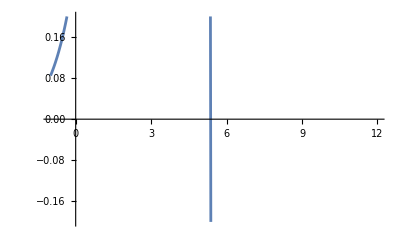

\left\{e^{t-4} \left(16 \sin \left(\frac{3}{2}-\frac{3 t}{8}\right)+9 \cos \left(\frac{3
   (t-4)}{8}\right)\right)\right\}

```mathematica
DE=64y''[t]-128*y'[t]+73 y[t]==0
IC={y[4]==9, y'[4]==3}
Gensol = DSolve[{DE, IC}, y[t], t]
Parsol=DSolve[{DE,IC},y[t],t]
DE/. Parsol[[1]]//Simplify
y[4]/. Parsol[[1]]
y'[4]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,12},PlotRange->{{-1,12},{-.2,.2}}]
```